```mathematica
data=Import[NotebookDirectory[]<>"output/profile_50mev.csv"];
```

```mathematica
mh=125.13;
v=174.;
μH2[mS_,sinθ_]:=1/2(mh^2(1-sinθ^2)+mS^2 sinθ^2);
μS2[mS_,sinθ_]:=sinθ^2 mh^2+(1-sinθ^2)mS^2;
A[mS_,sinθ_]:=((mh^2-mS^2)sinθ √(1-sinθ^2))/(√2 v);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
```

```mathematica
Snume[h_]:=Interpolation[data][h]
```

```mathematica
Snume[2]
```

-91716.7

```mathematica
Sana[h_]:=A[0.05,0.0012]/(2μS2[0.05,0.0012])(h^2+1/3*35.2325^2-2 v^2)
```

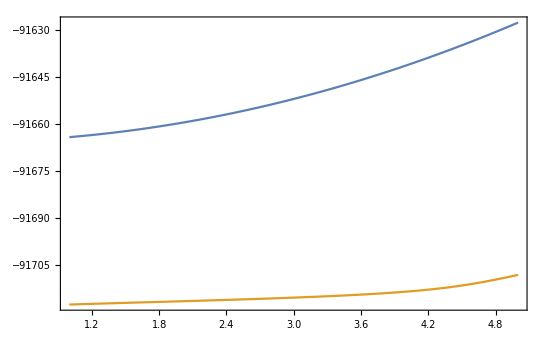

```mathematica
Plot[{Sana[h],Snume[h]},{h,1,5}]
```